## Figure 1: ReachPointFastest.pdf

```mathematica
Manipulate[Module[{mVs=1.5,v0,vG,p0,pV,pG,pGv, tspecial,tspecial2 ,nans,times,myTime,myTheta,p0x, v0x,p0y ,v0y,myThetaN,myTimeN,te
},
{p0,pV,pG} = loc;
v0 =pV-p0; (*compute the initial velocity*)
If[ locOld=== loc , ,
If[ Norm[v0]>mVs, v0= Normalize[v0]*mVs; loc⟦2⟧ =p0+v0; ]; (*Limit the initial velocity*)
locOld=loc; 
];
tspecial =      Norm[v0]/mA;      (*time when reachable set expands in every direction*)
tspecial2 = 2 Norm[v0]/mA;      (*time when reachable set covers NEW area in every direction.  *)

(*{myTheta,myTime}=reachPointFastest[pG,p0,v0,mA];*)
{myTheta,myTime}=reachPointFastestNum[pG,p0,v0,mA];
(*the locus of positions at the time when reachable set expands in every direction is drawn in orange. 
The locus of points when the reachable set contains p0 is in green.
The locus of positions that reaches the goal position is drawn in red. *)
Show[ParametricPlot[{posConstAccel[p0,v0,θ,t,mA],posConstAccel[p0,v0,θ,tspecial,mA],posConstAccel[p0,v0,θ,tspecial2,mA],posConstAccel[p0,v0,θ,myTime,mA]},{θ,-π,π},
Prolog-> {Gray,Table[te = 10*√(k/100);{Opacity[0.3],GrayLevel[(k+10)/120],Circle[ p0+te*v0, 1/2  mA te^2  ]},{k,100,1,-1}]},
(*posConstAccel[{p0x_,p0y_},{v0x_,v0y_},θ_,t_,mA_]:= {p0x+v0x*t+1/2 mA Cos[θ] t^2,
p0y+v0y*t+1/2  mA Sin[θ] t^2}*)

Epilog->{PointSize[Medium],Blue,Arrow[{p0,p0+v0}], Point[p0],
Blue,FontSize->20,
Text[StringForm["p(0)= `` m, v(0)= `` m/s",p0//MatrixForm,Round[v0,0.01]//MatrixForm],{0,3.5}],
Darker[Green],Point[pG],Red,
Text[StringForm["a_m= `` m/s 
at angle `` radians,
reaches goal at `` s",mA,Round[myTheta,0.01],Round[myTime,0.01]],{1,-3.5}],
 Purple,Arrow[{posConstAccel[p0,v0,myTheta,myTime,mA],
posConstAccel[p0,v0,myTheta,myTime,mA]+ v0+{Cos[myTheta],Sin[myTheta]}myTime
}]
},ImageSize->Medium,
AxesOrigin->{0,0},PlotRange->{{-5,5},{-5,5}}],
ParametricPlot[  posConstAccel[p0,v0,myTheta,t,mA],{t,0,myTime},PlotStyle->Red]
]
],
{{mA,0.5},0.1,2},{t,0,10},
(*       p0       pV      pg*)
{{loc,{{-4,1},{-3,1},{-2.5,-1.5}}},{-5,-5},{5,5},(*Locator*)ControlType->None,Appearance->None},{locOld, -1,ControlType->None}
]
```

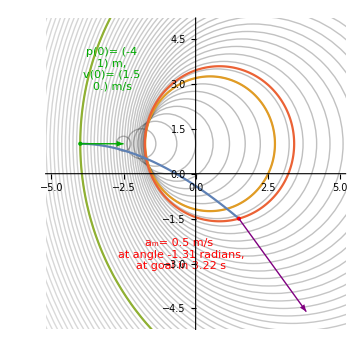
```mathematica
-Graphics--Graphics-
```

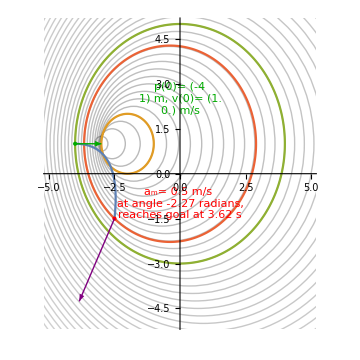
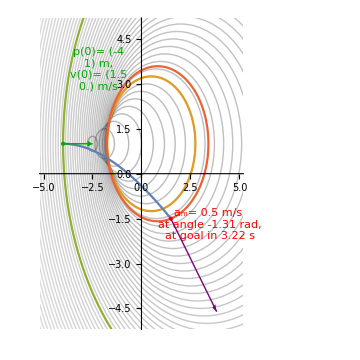
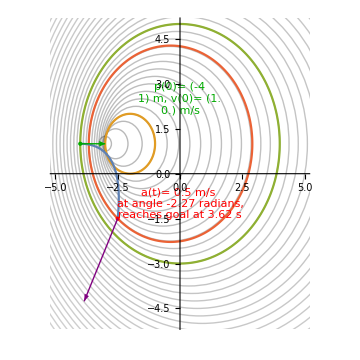
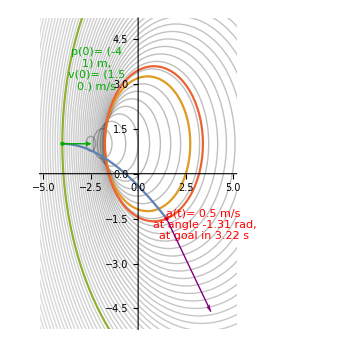

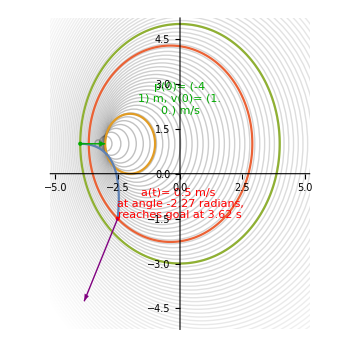
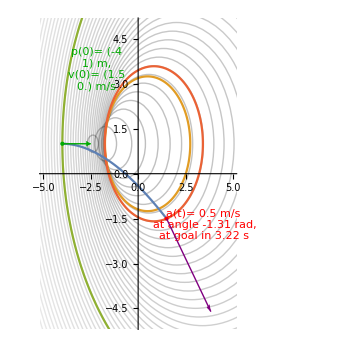

## Figure 1 : ReachPointFastest2.pdf

```mathematica
Manipulate[Module[{mVs=1.5,v0,vG,p0,pV,pG,pGv, tspecial,tspecial2 ,nans,times,myTime,myTheta,p0x, v0x,p0y ,v0y,myThetaN,myTimeN,te
},
{p0,pV,pG} = loc;
v0 =pV-p0; (*compute the initial velocity*)
If[ locOld=== loc , ,
If[ Norm[v0]>mVs, v0= Normalize[v0]*mVs; loc⟦2⟧ =p0+v0; ]; (*Limit the initial velocity*)
locOld=loc; 
];
tspecial =      Norm[v0]/mA;      (*time when reachable set expands in every direction*)
tspecial2 = 2 Norm[v0]/mA; (*time when reachable set covers NEW area in every direction.  *)

(*{myTheta,myTime}=reachPointFastest[pG,p0,v0,mA];*)
{myTheta,myTime}=reachPointFastestNum[pG,p0,v0,mA];
(*the locus of positions at the time when reachable set expands in every direction is drawn in orange. 
 The locus of points when the reachable set contains p0 is in green.
The locus of positions that reaches the goal position is drawn in red. *)
Show[ParametricPlot[{posConstAccel[p0,v0,θ,t,mA],posConstAccel[p0,v0,θ,tspecial,mA],posConstAccel[p0,v0,θ,tspecial2,mA],posConstAccel[p0,v0,θ,myTime,mA]},{θ,-π,π},
(*Prolog-> {Gray,Table[te = 3*tspecial*√(k/70);{Opacity[0.3],GrayLevel[(k+10)/80],Circle[ p0+te*v0, 1/2  mA te^2  ]},{k,70,1,-1}]},*)
Prolog-> {Gray,Table[te = 10*√(k/100);{Opacity[0.3],GrayLevel[(k+10)/120],Circle[ p0+te*v0, 1/2  mA te^2  ]},{k,100,1,-1}]},

Epilog->{PointSize[Medium],Blue,Arrow[{p0,p0+v0}], Point[p0],
FontSize->20,
Text[StringForm["p(0)= `` m,
v(0)= `` m/s",p0//MatrixForm,Round[v0,0.01]//MatrixForm],{-2.9,3.5}],
Darker[Green],Point[pG],
Text[StringForm["a_m= `` m/s 
at angle `` radians,
at goal in `` s",mA,Round[myTheta,0.01],Round[myTime,0.01]],{-.5,-2.7}],

 Purple,Arrow[{posConstAccel[p0,v0,myTheta,myTime,mA],
posConstAccel[p0,v0,myTheta,myTime,mA]+ v0+{Cos[myTheta],Sin[myTheta]}myTime
}]
},ImageSize->Medium,
AxesOrigin->{0,0},PlotRange->{{-5,5},{-5,5}}],
ParametricPlot[  posConstAccel[p0,v0,myTheta,t,mA],{t,0,myTime},PlotStyle->Red]
]
],
{{mA,0.5},0.1,2},{t,0,10},
(*       p0       pV      pg*)
{{loc,{{-4,1},{-2,1},{1.5,-1.5}}},{-5,-5},{5,5},(*Locator*)ControlType->None,Appearance->None},{locOld, -1,ControlType->None}
]
```

```mathematica
posConstAccel[{p0x_,p0y_},{v0x_,v0y_},θ_,t_,mA_]:= {p0x+v0x*t+1/2 mA Cos[θ] t^2,
p0y+v0y*t+1/2  mA Sin[θ] t^2}

posStopAndGo[{p0x_,p0y_},{v0x_,v0y_},θ_,t_,mA_]:=Module[{s0 = √(v0x^2+v0y^2),t1,p1x,p1y}, 
t1 = s0/mA;
{p1x,p1y} = {p0x,p0y}+1/2{v0x,v0y}*t1;
If[t<s0/mA, 
 {p0x+v0x*t-1/2 mA v0x/s0 t^2,
p0y+v0y*t-1/2  mA v0y/s0 t^2},
{p1x+1/2 mA Cos[θ](t-t1)^2,
p1y+1/2  mA Sin[θ](t-t1)^2}]]

pos2accel[{p0x_,p0y_},{v0x_,v0y_},θ1_,t1_,θ2_,t_,mA_]:=Module[{s0 = √(v0x^2+v0y^2),p1x,p1y}, 
If[t<t1, 
{p0x+v0x*t+1/2 mA Cos[θ1] t^2,
p0y+v0y*t+1/2  mA Sin[θ1] t^2},
{p0x+v0x*t+1/2 mA Cos[θ1] t1^2  +  t1*mA Cos[θ1](t-t1) +1/2 mA Cos[θ2](t-t1)^2  ,
p0y+v0y*t+1/2  mA Sin[θ1] t1^2+ t1* mA Sin[θ1](t-t1) +1/2 mA Sin[θ2](t-t1)^2 }]]


reachPointFastest[pG_,p0_,v0_,mA_]:=Module[{p0x,p0y,v0x,v0y,times,myTime,myTheta},
(*Solve for the fastest we can reach the goal point vG using constant acceleration of magnitude mA if we start at p0 with velocity v0.*)
{p0x,p0y}=pG-p0;
{v0x,v0y}=v0;
If[p0x==0 && p0y == 0, {0,0} (*ArcTan is undefined for this*),
times = Flatten[NSolve[mA^2 tv^4==4( (p0x-tv v0x)^2+(p0y-tv v0y)^2),{tv},Reals][[;;,;;,2]]];
(*times = Flatten[NSolve[tv (mA^2 tv^3+8 p0x *v0x+8 p0y *v0y)==4 (p0x^2+p0y^2+tv^2 (v0x^2+v0y^2)),{tv},Reals][[;;,;;,2]]];*)
(*Print[times];*)
myTime =  Min[Cases[times,x_/;x≥ 0]]; (*Pick smallest value*)
myTheta =ArcTan[p0x-myTime *v0x,p0y-myTime* v0y];
{myTheta,myTime}]
(*
W.l.o.g, transform coordinates so that pG is the origin.
The time $t$ is when the distance from the unforced circle center to $p_G$ is the length of the radius $\frac{1}{2} a_m t^2$.If the $p_G$ is the origin,this results in
\begin{align}
     \left(\frac{1}{2} a_m t^2\right)^2&=(p_{0x}-t v_{0x})^2+(p_{0y}-t v_{0y})^2,
\end{align}
which is a quartic in $t$.The smallest real solution greater than zero is the solution.If we rotate the coordinate frame so $v_{0y}=0$,and divide the velocity
and positions by $a_M$,we remove a constant.The four roots are simplified by the coefficients $c_1$ to $c_5$:

*)(*TODO: instead, find the 4 roots in tv of this equation

If we rotate the coordinate frame so v0y = 0, and divide the velocity and positions by mA,  The four roots are

c1 = (9 (p0x^2-2 p0y^2) v0x^2-2 v0x^6+3 √(12 (p0x^2+p0y^2)^3-3 (p0x^4+20 p0x^2 p0y^2-8 p0y^4) v0x^4+12 p0y^2 v0x^8))^(1/3);
c2 = 2*2^(1/3) (3 (p0x^2+p0y^2)-v0x^4);
c4 = √(4 v0x^2+-c2/c1+2^(2/3) c1);
c3 = (8 v0x^2+c2/c1-2^(2/3) c1+(12 √6 p0x v0x)/c4);
c5 = (8 v0x^2+c2/c1-2^(2/3) c1-(12 √6 p0x v0x)/c4);
1/(√6)(c4-c5) (*Root 1*)
1/(√6)(c4+c5)(*Root 2*)
-1/(√6)(c4+c3)(*Root 3*)
-1/(√6)(c4-c3)(*Root 4*)
*)
]

reachPointFastestNum[pG_,p0_,v0_,mA_]:=Module[{p0xT,p0yT,v0xIn,v0yIn,vx0Trans,
p0x,p0y,v0x,
solθ,solt,ϕ,p0Trans,p0TransRot,c1,c2,c3,c4,c5,myTimes},
(*Solve for the fastest we can reach the goal point vG using constant acceleration of magnitude mA if we start at p0 with velocity v0.
Returns {angleForAcceleration, timeForAcceleration} *)
{p0xT,p0yT} =pG-p0;
{v0xIn,v0yIn}=v0;
If[p0xT==0 && p0yT== 0, {0,0} (*ArcTan is undefined for this*),
vx0Trans =√(v0xIn^2+v0yIn^2) ;
If[vx0Trans==0,(*Special case: 0 velocity *)
solθ=ArcTan[-p0xT,-p0yT];
solt =  √((√(p0xT^2+p0yT^2))/(2 mA));
,
(*rotate so velocity points along x-axis*)
ϕ = -ArcTan[v0⟦1⟧,v0⟦2⟧];
p0TransRot = {
Cos[ϕ]*p0xT-Sin[ϕ]*p0yT,
 Sin[ϕ]*p0xT+Cos[ϕ]*p0yT};
(*Remove mA*)
{p0x,p0y}=p0TransRot/mA;
v0x = vx0Trans/mA;

myTimes = Flatten[NSolve[tv^4==4( (p0x-tv v0x)^2+p0y^2),{tv},Reals][[;;,;;,2]]];
solt =  Min[Cases[myTimes,x_/;x≥ 0]];  (*NSolve always works.  Finding the roots directly causes problems.*)
(*
(*Solve for roots.  This works almost all the time.... but not always. *)
c1 = (9 (p0x^2-2 p0y^2) v0x^2-2 v0x^6+3 √(12 (p0x^2+p0y^2)^3-3 (p0x^4+20 p0x^2 p0y^2-8 p0y^4) v0x^4+12 p0y^2 v0x^8))^(1/3);
c2 = 2*2^(1/3) (3 (p0x^2+p0y^2)-v0x^4);
c4 = √(4 v0x^2+-c2/c1+2^(2/3) c1);
c3 = (8 v0x^2+c2/c1-2^(2/3) c1+(12 √6 p0x v0x)/c4);
c5 = (8 v0x^2+c2/c1-2^(2/3) c1-(12 √6 p0x v0x)/c4);
Print[StringForm["c1=``, c4 = ``",c1,c4]];
myTimes ={};
If[c5≥0,myTimes= Join[myTimes,1/(√6){(c4-√c5) (*root 1*),(c4+√c5)(*Root 2*)}]];
If[c3≥0,myTimes= Join[myTimes,1/(√6){-(√c3+c4)(*Root 3*),(√c3-c4)(*Root 4*)}]];
Print[myTimes];
(*Print[Cases[myTimes,x_/;Im[x]==0&&x≥ 0]];*)
solt =  Re[Min[Cases[myTimes,x_/;Abs[Im[x]]<0.001&&Re[x]≥ 0]]];
*)

solθ =ArcTan[p0xT-solt *v0xIn,p0yT-solt* v0yIn];

];
{solθ,solt}
]
]
```

```mathematica
Timing[reachPointFastestNum[{-2,3},{3,2},{0.2,0.5},1/2]]
Timing[reachPointFastest[{-2,3},{3,2},{0.2,0.5},1/2]]
```

{0.001271,{-2.89874,4.96999}}

{0.001034,{-2.89874,4.96999}}

```mathematica
vals ={ 32.2+32ⅈ, -20,43}
Cases[vals,x_/;Im[x]==0&&x≥ 0 ]
```

{32.2+32. ⅈ,-20,43}

{43}

### Testing

```mathematica
(*reachPointFastest[pG,p0,v0,mA]*)
reachPointFastest[{2,5},{-2,4},{1,-.3},1/2]

(*posConstAccel[{p0x_,p0y_},{v0x_,v0y_},θ_,t_,mA_]*)
posConstAccel[{4,2},{-2,3},2.1,4,1/2]
```

{1.0576,2.93946}

{-6.01938,17.4528}

```mathematica
Clear[t]
Collect[Expand[t^4==4( (p0x-t v0x)^2+p0y^2)],t]
```

t^4==4 p0x^2+4 p0y^2-8 p0x t v0x+4 t^2 v0x^2

### Compare strategies (multi-stage trajectories, starting and stopping, and constant acceleration). These prove through reachability that it is never faster to use a multi-stage approach -- you should instead always accelerate at a constant heading to reach the goal fastest.

```mathematica
Manipulate[Module[{mVs=1.5,v0,vG,p0,pV,pG,pGv, nans,times,myTime,myTheta,p0x, v0x,p0y ,v0y,myThetaN,myTimeN,te
},
{p0,pV,pG} = loc;
v0 =pV-p0; (*compute the initial velocity*)
If[ locOld=== loc , ,
If[ Norm[v0]>mVs, v0= Normalize[v0]*mVs; loc⟦2⟧ =p0+v0; ]; (*Limit the initial velocity*)
locOld=loc; 
];
(*{myTheta,myTime}=reachPointFastest[pG,p0,v0,mA];*)
{myTheta,myTime}=reachPointFastestNum[pG,p0,v0,mA];
(*the locus of positions at the time when reachable set expands in every direction is drawn in orange. 
The locus of points when the reachable set contains p0 is in green.
The locus of positions that reaches the goal position is drawn in red. *)
Show[ParametricPlot[{posConstAccel[p0,v0,θ,t,mA],
pos2accel[p0,v0,θ1,t1,θ,t,mA]
},{θ,-π,π},PlotStyle->{Orange,Red},
Prolog->{Orange,{Opacity[0.2],Disk[p0+v0*t,mA/2 t^2]},Text["Reachable set
one acceleration",p0+v0*t],Brown,If[t> Norm[v0]/mA,{{Opacity[0.2], Disk[p0+v0*Norm[v0]/(2mA),mA/2(t-Norm[v0]/mA)^2]},Text["Reachable set
stop & go",p0+v0*Norm[v0]/(2mA)]}]},

Epilog->{PointSize[Medium],Blue,Arrow[{p0,p0+v0}], Point[p0],If[t<Norm[v0]/mA,{Brown,Point[p0+v0*t-(mA*v0)/(2 Norm[v0])t^2]}],
FontSize->12,Darker[Green],Point[pG],
 Purple,Arrow[{posConstAccel[p0,v0,myTheta,t,mA],
posConstAccel[p0,v0,myTheta,t,mA]+ v0+{Cos[myTheta],Sin[myTheta]}t}],
Brown, Arrow[{posConstAccel[p0,v0,myTheta,t,mA],
posConstAccel[p0,v0,myTheta,t,mA]+ mA{Cos[myTheta],Sin[myTheta]}}]
},ImageSize->Medium,
AxesOrigin->{0,0},PlotRange->{{-5,5},{-5,5}}],
ParametricPlot[  posConstAccel[p0,v0,myTheta,t,mA],{t,0,myTime},PlotStyle->Red]
]
],
{{mA,0.5},0.1,2},
{{t1,10},0,10},
{θ1,0,2π},
{t,0,10},
(*       p0       pV      pg*)
{{loc,{{-4,1},{-3,1},{-2.5,-1.5}}},{-5,-5},{5,5},Locator(*ControlType->None*),Appearance->None},{locOld, -1,ControlType->None}
]
```

```mathematica
Manipulate[Module[{mVs=1.5,v0,vG,p0,pV,pG,pGv, nans,times,myTime,myTheta,p0x, v0x,p0y ,v0y,myThetaN,myTimeN,te
},
{p0,pV,pG} = loc;
v0 =pV-p0; (*compute the initial velocity*)
If[ locOld=== loc , ,
If[ Norm[v0]>mVs, v0= Normalize[v0]*mVs; loc⟦2⟧ =p0+v0; ]; (*Limit the initial velocity*)
locOld=loc; 
];
(*{myTheta,myTime}=reachPointFastest[pG,p0,v0,mA];*)
{myTheta,myTime}=reachPointFastestNum[pG,p0,v0,mA];
(*the locus of positions at the time when reachable set expands in every direction is drawn in orange. 
The locus of points when the reachable set contains p0 is in green.
The locus of positions that reaches the goal position is drawn in red. *)
Show[ParametricPlot[{posConstAccel[p0,v0,θ,t,mA],
posStopAndGo[p0,v0,θ,t,mA]
},{θ,-π,π},PlotStyle->{Orange,Brown},
Prolog->{Orange,{Opacity[0.2],Disk[p0+v0*t,mA/2 t^2]},Text["Reachable set
one acceleration",p0+v0*t],Brown,If[t> Norm[v0]/mA,{{Opacity[0.2], Disk[p0+v0*Norm[v0]/(2mA),mA/2(t-Norm[v0]/mA)^2]},Text["Reachable set
stop & go",p0+v0*Norm[v0]/(2mA)]},Point[p0]]},
Epilog->{PointSize[Medium],Darker[Green],Arrow[{p0,p0+v0}], Point[p0],
FontSize->12,Red,Point[pG],
 Purple,Arrow[{posConstAccel[p0,v0,myTheta,myTime,mA],
posConstAccel[p0,v0,myTheta,myTime,mA]+ v0+{Cos[myTheta],Sin[myTheta]}myTime
}]
},ImageSize->Medium,
AxesOrigin->{0,0},PlotRange->{{-5,5},{-5,5}}],
ParametricPlot[  posConstAccel[p0,v0,myTheta,t,mA],{t,0,myTime}]
]
],
{{mA,0.5},0.1,2},{t,0,10},
(*       p0       pV      pg*)
{{loc,{{-4,1},{-3,1},{-2.5,-1.5}}},{-5,-5},{5,5},Locator(*ControlType->None*),Appearance->None},{locOld, -1,ControlType->None}
]
```